```mathematica
Get[FileNameJoin[{NotebookDirectory[], "functions.m"}]]
```

```mathematica
b1 = MergeDirections["1_Danestone_RGU.txt", "1_RGU_Danestone.txt"];
b2 = MergeDirections["2_Ashwood_RGU.txt", "2_RGU_Ashwood.txt"];
b3 = MergeDirections["3_Cove_Mastrick.txt", "3_Mastrick_Cove.txt"];
b11 = MergeDirections["11_Northfield_Woodend.txt", "11_Woodend_Northfield.txt"];
b12 = MergeDirections["12_Heathryfold_Torry.txt", "12_Torry_Heathryfold.txt"];
b13 = MergeDirections["13_Golf_Links_Scatterburn.txt", "13_Scatterburn _Golf_Links.txt"];
b15 = MergeDirections["15_Balnagask_Circle_Countesswells.txt", "15_Countesswells_Balnagask_Circle.txt"];
b17 = MergeDirections["17_Dyce_Faulds_Gate.txt", "17_Faulds_Gate_Dyce.txt"];
b18 = MergeDirections["18_Dyce_Redmoss.txt", "18_Redmoss_Dyce.txt"];
b19 = MergeDirections["19_Culter_Tillydrone.txt", "19_Tillydrone_Culter.txt"];
b20 = MergeDirections["20_Guild_str_Hillhead.txt", "20_Hillhead_Guild_str.txt"];
b23 = MergeDirections["23_Raasay_Gardens_Heathryfold.txt",  "23_Heathryfold_Raasay_Gardens.txt"];
```

```mathematica
buses = {b1, b3, b11, b12, b13, b15, b17, b18, b19, b20, b23};
routeNames = {"1", "3", "11", "12", "13", "15", "17", "18", "19", "20", "23"};
```

```mathematica
TAPs=Algorithm821[buses, routeNames, Quantity[15, "Minutes"]];
```

```mathematica
Max[#[[2]]&/@Values[TAPs[[3]]]]
```

1

```mathematica
mtx =MatrixFromPetriNet[TAPs[[1]], TAPs[[2]], TAPs[[3]]];
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

121

122

```mathematica
Dimensions[mtx]
```

{122,122}

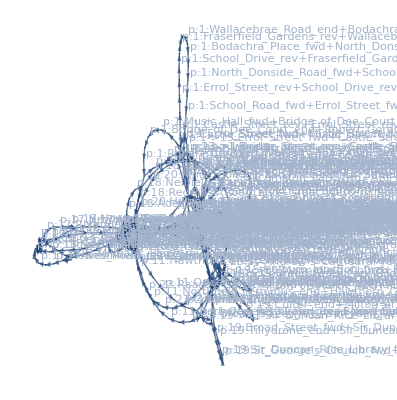

```mathematica
CreatePetriNetFromTAPs[TAPs]
```

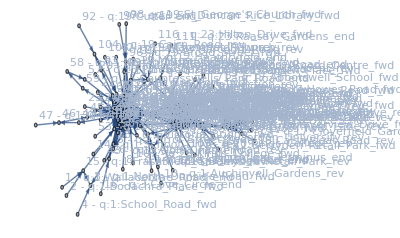

```mathematica
MakeAdjacencyGraph[mtx, TAPs]
```

```mathematica
v = MakeStateVector[mtx]
```

{-∞,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,-∞,0,0,-∞,0,-∞,0,0,-∞,0,0,-∞,-∞,0,-∞,0,0,0,-∞,-∞,0,0,0,-∞,0,0,0,-∞,0,-∞,0,-∞,0,0,0,0,0,-∞,0,-∞,-∞,0,-∞,0,0,-∞,0,-∞,0,0,-∞,-∞,0,-∞,0,-∞,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,-∞,0,0,0,0,-∞,-∞,0,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,-∞,0,0,-∞,0,0,-∞,0,-∞,0}

```mathematica
Count[v, 0]
```

70

```mathematica
ttb = TimeTable[mtx,v, TAPs[[1]], 10];
```

```mathematica
ttb // Transpose // MatrixForm
```

(q:1:Wallacebrae_Road_end | -∞ | 13. | 25. | 67. | 97. | 131. | 161. | 195. | 225. | 259.
q:1:Bodachra_Place_fwd | -∞ | 20. | 32. | 74. | 104. | 138. | 168. | 202. | 232. | 266.
q:1:North_Donside_Road_fwd | 0 | 27. | 39. | 81. | 111. | 145. | 175. | 209. | 239. | 273.
q:1:School_Road_fwd | -∞ | 7. | 34. | 46. | 88. | 118. | 152. | 182. | 216. | 246.
q:1:Errol_Street_fwd | 0 | 12. | 39. | 51. | 93. | 123. | 157. | 187. | 221. | 251.
q:1:Castle_Street_fwd | -∞ | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294.
q:1:Music_Hall_fwd | 0 | 43. | 73. | 107. | 137. | 171. | 201. | 235. | 265. | 299.
q:1:Bridge_of_Dee_Court_end | -∞ | 14. | 57. | 87. | 121. | 151. | 185. | 215. | 249. | 279.
q:1:Robert_Gordon_University_rev | 0 | 18. | 61. | 91. | 125. | 155. | 189. | 219. | 253. | 283.
q:1:Auchinyell_Gardens_rev | -∞ | 8. | 26. | 69. | 99. | 133. | 163. | 197. | 227. | 261.
q:1:Great_Western_Road_rev | 0 | 23. | 34. | 77. | 107. | 141. | 171. | 205. | 235. | 269.
q:1:Castle_Street_rev | -∞ | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294.
q:1:Errol_Street_rev | 0 | 42. | 72. | 106. | 136. | 170. | 200. | 234. | 264. | 298.
q:1:School_Drive_rev | -∞ | 5. | 47. | 77. | 111. | 141. | 175. | 205. | 239. | 269.
q:1:Fraserfield_Gardens_rev | 0 | 12. | 54. | 84. | 118. | 148. | 182. | 212. | 246. | 276.
q:3:Cove_Circle_end | -∞ | 9. | 18. | 50. | 70. | 114. | 144. | 178. | 208. | 242.
q:3:Altens_Farm_Road_fwd | 0 | 19. | 28. | 60. | 80. | 124. | 154. | 188. | 218. | 252.
q:3:Victoria_Bridge_fwd | -∞ | 25. | 57. | 87. | 121. | 151. | 185. | 215. | 249. | 279.
q:3:Guild_Street_fwd | 0 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288.
q:3:Gilcomston_Park_fwd | -∞ | 6. | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260.
q:3:ARI_Bus_Port_fwd | 0 | 17. | 49. | 79. | 113. | 143. | 177. | 207. | 241. | 271.
q:3:Mastrick_end | 0 | 10. | 27. | 59. | 89. | 123. | 153. | 187. | 217. | 251.
q:3:Aberdeen_Royal_Infirmary_rev | -∞ | 9. | 19. | 36. | 68. | 98. | 132. | 162. | 196. | 226.
q:3:Bridge_Street_rev | -∞ | 19. | 46. | 78. | 108. | 142. | 172. | 206. | 236. | 270.
q:3:Guild_Street_rev | 0 | 32. | 52. | 96. | 126. | 160. | 190. | 224. | 254. | 288.
q:3:Altens_Farm_Road_rev | 0 | 9. | 41. | 61. | 105. | 135. | 169. | 199. | 233. | 263.
q:11:Northfield_Terminus_end | -∞ | 23. | 38. | 73. | 105. | 135. | 169. | 199. | 233. | 263.
q:11:Hawthorn_Crescent_fwd | 0 | 31. | 46. | 81. | 113. | 143. | 177. | 207. | 241. | 271.
q:11:Berryden_Retail_Park_fwd | -∞ | 9. | 40. | 55. | 90. | 122. | 152. | 186. | 216. | 250.
q:11:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268.
q:11:Queen's_Cross_fwd | 0 | 12. | 33. | 63. | 88. | 118. | 152. | 182. | 216. | 246.
q:11:Woodend_end | -∞ | 8. | 20. | 41. | 71. | 96. | 126. | 160. | 190. | 224.
q:11:Queen's_Cross_rev | 0 | 16. | 28. | 49. | 79. | 104. | 134. | 168. | 198. | 232.
q:11:Broad_Street_rev | 0 | 15. | 50. | 82. | 112. | 146. | 176. | 210. | 240. | 274.
q:11:Berryden_Retail_Park_rev | -∞ | 11. | 26. | 61. | 93. | 123. | 157. | 187. | 221. | 251.
q:12:Heathryfold_end | -∞ | 24. | 56. | 86. | 120. | 150. | 184. | 214. | 248. | 278.
q:12:Belmont_Road_fwd | 0 | 36. | 68. | 98. | 132. | 162. | 196. | 226. | 260. | 290.
q:12:Bridge_Street_fwd | -∞ | 19. | 46. | 78. | 108. | 142. | 172. | 206. | 236. | 270.
q:12:Guild_Street_fwd | 0 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288.
q:12:Torry_Terminus_end | 0 | 10. | 42. | 72. | 106. | 136. | 170. | 200. | 234. | 264.
q:12:Guild_Street_rev | 0 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288.
q:12:Chestnut_Row_rev | -∞ | 14. | 46. | 76. | 110. | 140. | 174. | 204. | 238. | 268.
q:13:Golf_Links_end | -∞ | 14. | 58. | 88. | 122. | 152. | 186. | 216. | 250. | 280.
q:13:Beach_Boulevard_fwd | 0 | 24. | 68. | 98. | 132. | 162. | 196. | 226. | 260. | 290.
q:13:St_Andrew's_Cathedral_fwd | 0 | 14. | 34. | 78. | 108. | 142. | 172. | 206. | 236. | 270.
q:13:Prince_Arthur_Street_fwd | 0 | 13. | 27. | 47. | 91. | 121. | 155. | 185. | 219. | 249.
q:13:Mastrick_Shops_fwd | -∞ | 15. | 28. | 42. | 62. | 106. | 136. | 170. | 200. | 234.
q:13:Turning_Circle_end | 0 | 24. | 37. | 51. | 71. | 115. | 145. | 179. | 209. | 243.
q:13:Summerhill_Terrace_rev | 0 | 15. | 39. | 52. | 66. | 86. | 130. | 160. | 194. | 224.
q:13:Bridge_Street_rev | 0 | 19. | 46. | 78. | 108. | 142. | 172. | 206. | 236. | 270.
q:13:Castle_Street_rev | -∞ | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294.
q:13:Beach_Boulevard_rev | 0 | 44. | 74. | 108. | 138. | 172. | 202. | 236. | 266. | 300.
q:15:Balnagask_Circle_end | -∞ | 14. | 46. | 76. | 110. | 140. | 174. | 204. | 238. | 268.
q:15:Victoria_Bridge_fwd | 0 | 25. | 57. | 87. | 121. | 151. | 185. | 215. | 249. | 279.
q:15:Guild_Street_fwd | -∞ | 30. | 62. | 92. | 126. | 156. | 190. | 220. | 254. | 284.
q:15:Holburn_Junction_fwd | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295.
q:15:Pinewood_Place_fwd | 0 | 15. | 56. | 88. | 118. | 152. | 182. | 216. | 246. | 280.
q:15:North_Countesswells_Road_fwd | 0 | 15. | 30. | 71. | 103. | 133. | 167. | 197. | 231. | 261.
q:15:Countesswells_Park_Road_end | 0 | 6. | 21. | 36. | 77. | 109. | 139. | 173. | 203. | 237.
q:15:Airyhall_rev | 0 | 15. | 21. | 36. | 51. | 92. | 124. | 154. | 188. | 218.
q:15:Holburn_Junction_rev | -∞ | 23. | 43. | 87. | 117. | 151. | 181. | 215. | 245. | 279.
q:15:Guild_Street_rev | 0 | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288.
q:17:Dyce_end | -∞ | 17. | 39. | 60. | 90. | 115. | 145. | 179. | 209. | 243.
q:17:Riverview_Drive_fwd | -∞ | 28. | 50. | 71. | 101. | 126. | 156. | 190. | 220. | 254.
q:17:Newhills_fwd | 0 | 36. | 58. | 79. | 109. | 134. | 164. | 198. | 228. | 262.
q:17:Howes_Road_fwd | -∞ | 10. | 46. | 68. | 89. | 119. | 144. | 174. | 208. | 238.
q:17:Mugiemoss_Road_fwd | 0 | 17. | 53. | 75. | 96. | 126. | 151. | 181. | 215. | 245.
q:17:Millbank_Place_fwd | 0 | 10. | 27. | 63. | 85. | 106. | 136. | 161. | 191. | 225.
q:17:Bon_Accord_Centre_fwd | -∞ | 6. | 16. | 33. | 69. | 91. | 112. | 142. | 167. | 197.
q:17:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268.
q:17:Abbotswell_School_fwd | -∞ | 13. | 34. | 64. | 89. | 119. | 153. | 183. | 217. | 247.
q:17:Faulds_Gate_end | 0 | 19. | 40. | 70. | 95. | 125. | 159. | 189. | 223. | 253.
q:17:Devanha_Gardens_rev | 0 | 11. | 30. | 51. | 81. | 106. | 136. | 170. | 200. | 234.
q:17:Adelphi_rev | -∞ | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268.
q:17:Bon_Accord_Centre_rev | -∞ | 25. | 55. | 80. | 110. | 144. | 174. | 208. | 238. | 272.
q:17:Millbank_Place_rev | 0 | 29. | 59. | 84. | 114. | 148. | 178. | 212. | 242. | 276.
q:17:Smithfield_Lane_rev | -∞ | 16. | 37. | 67. | 92. | 122. | 156. | 186. | 220. | 250.
q:17:Howes_Road_rev | 0 | 22. | 43. | 73. | 98. | 128. | 162. | 192. | 226. | 256.
q:17:Cloverfield_Gardens_rev | -∞ | 8. | 30. | 51. | 81. | 106. | 136. | 170. | 200. | 234.
q:18:Dyce_end | -∞ | 17. | 39. | 60. | 90. | 115. | 145. | 179. | 209. | 243.
q:18:Riverview_Drive_fwd | 0 | 28. | 50. | 71. | 101. | 126. | 156. | 190. | 220. | 254.
q:18:Mugiemoss_Road_fwd | 0 | 17. | 53. | 75. | 96. | 126. | 151. | 181. | 215. | 245.
q:18:Powis_Lane_fwd | -∞ | 10. | 27. | 63. | 85. | 106. | 136. | 161. | 191. | 225.
q:18:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268.
q:18:Nellfield_Place_fwd | 0 | 10. | 31. | 61. | 86. | 116. | 150. | 180. | 214. | 244.
q:18:Redmoss_Road_end | -∞ | 11. | 21. | 42. | 72. | 97. | 127. | 161. | 191. | 225.
q:18:Great_Western_Road_rev | 0 | 23. | 34. | 77. | 107. | 141. | 171. | 205. | 235. | 269.
q:18:Adelphi_rev | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268.
q:18:Calsayseat_Road_rev | -∞ | 7. | 28. | 58. | 83. | 113. | 147. | 177. | 211. | 241.
q:18:Smithfield_Lane_rev | 0 | 16. | 37. | 67. | 92. | 122. | 156. | 186. | 220. | 250.
q:18:Riverview_Drive_rev | 0 | 21. | 43. | 64. | 94. | 119. | 149. | 183. | 213. | 247.
q:19:Culter_end | -∞ | 13. | 35. | 76. | 108. | 138. | 172. | 202. | 236. | 266.
q:19:Milton_of_Murtle_fwd | 0 | 27. | 49. | 90. | 122. | 152. | 186. | 216. | 250. | 280.
q:19:Mannofield_Church_fwd | 0 | 15. | 42. | 64. | 105. | 137. | 167. | 201. | 231. | 265.
q:19:Holburn_Junction_fwd | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295.
q:19:Broad_Street_fwd | 0 | 10. | 50. | 82. | 112. | 146. | 176. | 210. | 240. | 274.
q:19:Sir_Duncan_Rice_Library_fwd | -∞ | 14. | 24. | 64. | 96. | 126. | 160. | 190. | 224. | 254.
q:19:St_George's_Church_fwd | -∞ | 17. | 27. | 67. | 99. | 129. | 163. | 193. | 227. | 257.
q:19:Tillydrone_end | 0 | 20. | 30. | 70. | 102. | 132. | 166. | 196. | 230. | 260.
q:19:Sir_Duncan_Rice_Library_rev | 0 | 8. | 28. | 38. | 78. | 110. | 140. | 174. | 204. | 238.
q:19:Broad_Street_rev | -∞ | 15. | 26. | 43. | 59. | 93. | 125. | 155. | 189. | 219.
q:19:Holburn_Junction_rev | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295.
q:19:Mannofield_Church_rev | -∞ | 11. | 52. | 84. | 114. | 148. | 178. | 212. | 242. | 276.
q:19:Cairn_Road_rev | 0 | 22. | 63. | 95. | 125. | 159. | 189. | 223. | 253. | 287.
q:20:Guild_Street_end | -∞ | 32. | 62. | 96. | 126. | 160. | 190. | 224. | 254. | 288.
q:20:Castle_Street_fwd | 0 | 38. | 68. | 102. | 132. | 166. | 196. | 230. | 260. | 294.
q:20:Kings_College_fwd | -∞ | 9. | 47. | 77. | 111. | 141. | 175. | 205. | 239. | 269.
q:20:Hillhead_Of_Seaton_end | 0 | 17. | 55. | 85. | 119. | 149. | 183. | 213. | 247. | 277.
q:20:Kings_College_rev | -∞ | 9. | 26. | 64. | 94. | 128. | 158. | 192. | 222. | 256.
q:20:Adelphi_rev | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268.
q:23:Raasay_Gardens_end | -∞ | 4. | 21. | 62. | 94. | 124. | 158. | 188. | 222. | 252.
q:23:Raeden_Avenue_fwd | 0 | 14. | 31. | 72. | 104. | 134. | 168. | 198. | 232. | 262.
q:23:Carden_Place_fwd | -∞ | 9. | 23. | 40. | 81. | 113. | 143. | 177. | 207. | 241.
q:23:Adelphi_fwd | 0 | 21. | 51. | 76. | 106. | 140. | 170. | 204. | 234. | 268.
q:23:Fraser_Place_fwd | 0 | 7. | 28. | 58. | 83. | 113. | 147. | 177. | 211. | 241.
q:23:Hilton_Drive_fwd | -∞ | 9. | 16. | 37. | 67. | 92. | 122. | 156. | 186. | 220.
q:23:Heathryfold_end | 0 | 24. | 56. | 86. | 120. | 150. | 184. | 214. | 248. | 278.
q:23:Hilton_Drive_rev | 0 | 11. | 35. | 67. | 97. | 131. | 161. | 195. | 225. | 259.
q:23:St_Andrew's_Cathedral_rev | -∞ | 14. | 34. | 78. | 108. | 142. | 172. | 206. | 236. | 270.
q:23:Holburn_Junction_rev | 0 | 41. | 73. | 103. | 137. | 167. | 201. | 231. | 265. | 295.
q:23:Harcourt_Road_rev | -∞ | 9. | 50. | 82. | 112. | 146. | 176. | 210. | 240. | 274.
q:23:Colonsay_Crescent_rev | 0 | 17. | 58. | 90. | 120. | 154. | 184. | 218. | 248. | 282.)

```mathematica
ExportMaxPlusMatrix["matrix_ct15", mtx]
```

```mathematica
routes = SplitByRoutes[ttb, routeNames];
```

```mathematica
ConvertToHoursTimetable[routes[[1]]] // MatrixForm
```

(q:1:Wallacebrae_Road_end | 06:13:00GMT+1TimeObject[{6,13,0},Instant,1.] | 06:25:00GMT+1TimeObject[{6,25,0},Instant,1.] | 07:07:00GMT+1TimeObject[{7,7,0},Instant,1.] | 07:37:00GMT+1TimeObject[{7,37,0},Instant,1.] | 08:11:00GMT+1TimeObject[{8,11,0},Instant,1.] | 08:41:00GMT+1TimeObject[{8,41,0},Instant,1.] | 09:15:00GMT+1TimeObject[{9,15,0},Instant,1.] | 09:45:00GMT+1TimeObject[{9,45,0},Instant,1.] | 10:19:00GMT+1TimeObject[{10,19,0},Instant,1.]
q:1:Bodachra_Place_fwd | 06:20:00GMT+1TimeObject[{6,20,0},Instant,1.] | 06:32:00GMT+1TimeObject[{6,32,0},Instant,1.] | 07:14:00GMT+1TimeObject[{7,14,0},Instant,1.] | 07:44:00GMT+1TimeObject[{7,44,0},Instant,1.] | 08:18:00GMT+1TimeObject[{8,18,0},Instant,1.] | 08:48:00GMT+1TimeObject[{8,48,0},Instant,1.] | 09:22:00GMT+1TimeObject[{9,22,0},Instant,1.] | 09:52:00GMT+1TimeObject[{9,52,0},Instant,1.] | 10:26:00GMT+1TimeObject[{10,26,0},Instant,1.]
q:1:North_Donside_Road_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:27:00GMT+1TimeObject[{6,27,0},Instant,1.] | 06:39:00GMT+1TimeObject[{6,39,0},Instant,1.] | 07:21:00GMT+1TimeObject[{7,21,0},Instant,1.] | 07:51:00GMT+1TimeObject[{7,51,0},Instant,1.] | 08:25:00GMT+1TimeObject[{8,25,0},Instant,1.] | 08:55:00GMT+1TimeObject[{8,55,0},Instant,1.] | 09:29:00GMT+1TimeObject[{9,29,0},Instant,1.] | 09:59:00GMT+1TimeObject[{9,59,0},Instant,1.]
q:1:School_Road_fwd | 06:07:00GMT+1TimeObject[{6,7,0},Instant,1.] | 06:34:00GMT+1TimeObject[{6,34,0},Instant,1.] | 06:46:00GMT+1TimeObject[{6,46,0},Instant,1.] | 07:28:00GMT+1TimeObject[{7,28,0},Instant,1.] | 07:58:00GMT+1TimeObject[{7,58,0},Instant,1.] | 08:32:00GMT+1TimeObject[{8,32,0},Instant,1.] | 09:02:00GMT+1TimeObject[{9,2,0},Instant,1.] | 09:36:00GMT+1TimeObject[{9,36,0},Instant,1.] | 10:06:00GMT+1TimeObject[{10,6,0},Instant,1.]
q:1:Errol_Street_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:12:00GMT+1TimeObject[{6,12,0},Instant,1.] | 06:39:00GMT+1TimeObject[{6,39,0},Instant,1.] | 06:51:00GMT+1TimeObject[{6,51,0},Instant,1.] | 07:33:00GMT+1TimeObject[{7,33,0},Instant,1.] | 08:03:00GMT+1TimeObject[{8,3,0},Instant,1.] | 08:37:00GMT+1TimeObject[{8,37,0},Instant,1.] | 09:07:00GMT+1TimeObject[{9,7,0},Instant,1.] | 09:41:00GMT+1TimeObject[{9,41,0},Instant,1.]
q:1:Castle_Street_fwd | 06:38:00GMT+1TimeObject[{6,38,0},Instant,1.] | 07:08:00GMT+1TimeObject[{7,8,0},Instant,1.] | 07:42:00GMT+1TimeObject[{7,42,0},Instant,1.] | 08:12:00GMT+1TimeObject[{8,12,0},Instant,1.] | 08:46:00GMT+1TimeObject[{8,46,0},Instant,1.] | 09:16:00GMT+1TimeObject[{9,16,0},Instant,1.] | 09:50:00GMT+1TimeObject[{9,50,0},Instant,1.] | 10:20:00GMT+1TimeObject[{10,20,0},Instant,1.] | 10:54:00GMT+1TimeObject[{10,54,0},Instant,1.]
q:1:Music_Hall_fwd | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:43:00GMT+1TimeObject[{6,43,0},Instant,1.] | 07:13:00GMT+1TimeObject[{7,13,0},Instant,1.] | 07:47:00GMT+1TimeObject[{7,47,0},Instant,1.] | 08:17:00GMT+1TimeObject[{8,17,0},Instant,1.] | 08:51:00GMT+1TimeObject[{8,51,0},Instant,1.] | 09:21:00GMT+1TimeObject[{9,21,0},Instant,1.] | 09:55:00GMT+1TimeObject[{9,55,0},Instant,1.] | 10:25:00GMT+1TimeObject[{10,25,0},Instant,1.]
q:1:Bridge_of_Dee_Court_end | 06:14:00GMT+1TimeObject[{6,14,0},Instant,1.] | 06:57:00GMT+1TimeObject[{6,57,0},Instant,1.] | 07:27:00GMT+1TimeObject[{7,27,0},Instant,1.] | 08:01:00GMT+1TimeObject[{8,1,0},Instant,1.] | 08:31:00GMT+1TimeObject[{8,31,0},Instant,1.] | 09:05:00GMT+1TimeObject[{9,5,0},Instant,1.] | 09:35:00GMT+1TimeObject[{9,35,0},Instant,1.] | 10:09:00GMT+1TimeObject[{10,9,0},Instant,1.] | 10:39:00GMT+1TimeObject[{10,39,0},Instant,1.]
q:1:Robert_Gordon_University_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:18:00GMT+1TimeObject[{6,18,0},Instant,1.] | 07:01:00GMT+1TimeObject[{7,1,0},Instant,1.] | 07:31:00GMT+1TimeObject[{7,31,0},Instant,1.] | 08:05:00GMT+1TimeObject[{8,5,0},Instant,1.] | 08:35:00GMT+1TimeObject[{8,35,0},Instant,1.] | 09:09:00GMT+1TimeObject[{9,9,0},Instant,1.] | 09:39:00GMT+1TimeObject[{9,39,0},Instant,1.] | 10:13:00GMT+1TimeObject[{10,13,0},Instant,1.]
q:1:Auchinyell_Gardens_rev | 06:08:00GMT+1TimeObject[{6,8,0},Instant,1.] | 06:26:00GMT+1TimeObject[{6,26,0},Instant,1.] | 07:09:00GMT+1TimeObject[{7,9,0},Instant,1.] | 07:39:00GMT+1TimeObject[{7,39,0},Instant,1.] | 08:13:00GMT+1TimeObject[{8,13,0},Instant,1.] | 08:43:00GMT+1TimeObject[{8,43,0},Instant,1.] | 09:17:00GMT+1TimeObject[{9,17,0},Instant,1.] | 09:47:00GMT+1TimeObject[{9,47,0},Instant,1.] | 10:21:00GMT+1TimeObject[{10,21,0},Instant,1.]
q:1:Great_Western_Road_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:23:00GMT+1TimeObject[{6,23,0},Instant,1.] | 06:34:00GMT+1TimeObject[{6,34,0},Instant,1.] | 07:17:00GMT+1TimeObject[{7,17,0},Instant,1.] | 07:47:00GMT+1TimeObject[{7,47,0},Instant,1.] | 08:21:00GMT+1TimeObject[{8,21,0},Instant,1.] | 08:51:00GMT+1TimeObject[{8,51,0},Instant,1.] | 09:25:00GMT+1TimeObject[{9,25,0},Instant,1.] | 09:55:00GMT+1TimeObject[{9,55,0},Instant,1.]
q:1:Castle_Street_rev | 06:38:00GMT+1TimeObject[{6,38,0},Instant,1.] | 07:08:00GMT+1TimeObject[{7,8,0},Instant,1.] | 07:42:00GMT+1TimeObject[{7,42,0},Instant,1.] | 08:12:00GMT+1TimeObject[{8,12,0},Instant,1.] | 08:46:00GMT+1TimeObject[{8,46,0},Instant,1.] | 09:16:00GMT+1TimeObject[{9,16,0},Instant,1.] | 09:50:00GMT+1TimeObject[{9,50,0},Instant,1.] | 10:20:00GMT+1TimeObject[{10,20,0},Instant,1.] | 10:54:00GMT+1TimeObject[{10,54,0},Instant,1.]
q:1:Errol_Street_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:42:00GMT+1TimeObject[{6,42,0},Instant,1.] | 07:12:00GMT+1TimeObject[{7,12,0},Instant,1.] | 07:46:00GMT+1TimeObject[{7,46,0},Instant,1.] | 08:16:00GMT+1TimeObject[{8,16,0},Instant,1.] | 08:50:00GMT+1TimeObject[{8,50,0},Instant,1.] | 09:20:00GMT+1TimeObject[{9,20,0},Instant,1.] | 09:54:00GMT+1TimeObject[{9,54,0},Instant,1.] | 10:24:00GMT+1TimeObject[{10,24,0},Instant,1.]
q:1:School_Drive_rev | 06:05:00GMT+1TimeObject[{6,5,0},Instant,1.] | 06:47:00GMT+1TimeObject[{6,47,0},Instant,1.] | 07:17:00GMT+1TimeObject[{7,17,0},Instant,1.] | 07:51:00GMT+1TimeObject[{7,51,0},Instant,1.] | 08:21:00GMT+1TimeObject[{8,21,0},Instant,1.] | 08:55:00GMT+1TimeObject[{8,55,0},Instant,1.] | 09:25:00GMT+1TimeObject[{9,25,0},Instant,1.] | 09:59:00GMT+1TimeObject[{9,59,0},Instant,1.] | 10:29:00GMT+1TimeObject[{10,29,0},Instant,1.]
q:1:Fraserfield_Gardens_rev | 06:00:00GMT+1TimeObject[{6,0,0.},Instant,1.] | 06:12:00GMT+1TimeObject[{6,12,0},Instant,1.] | 06:54:00GMT+1TimeObject[{6,54,0},Instant,1.] | 07:24:00GMT+1TimeObject[{7,24,0},Instant,1.] | 07:58:00GMT+1TimeObject[{7,58,0},Instant,1.] | 08:28:00GMT+1TimeObject[{8,28,0},Instant,1.] | 09:02:00GMT+1TimeObject[{9,2,0},Instant,1.] | 09:32:00GMT+1TimeObject[{9,32,0},Instant,1.] | 10:06:00GMT+1TimeObject[{10,6,0},Instant,1.])